```mathematica
globalPoints = {}; 
updateGlobals[points_] := ( 
 globalPoints = Join[globalPoints, {points}]; 
 Print[globalPoints];
);
DynamicModule[{p = {}, pts = {}, showModule = True},
 Column[{
   If[showModule,
    EventHandler[
     Dynamic@Graphics[{Point[p], Circle[{0, 0}, 1]}, PlotRange → {{-1.5, 1.5}, {-1.5, 1.5}}, Frame → True, Axes → True, AspectRatio → 1, ImageSize → 700], 
     "MouseDown" :> (
     pt = MousePosition["Graphics"];
       AppendTo[p, pt/Norm[pt]];
       AppendTo[pts, pt/Norm[pt]];
       If[Length[pts]==2, 
     theta = Input["Enter bending angle for the chosen pair"];
     AppendTo[pts, theta];
     updateGlobals[pts];
     pts = {};
     ];
     )
    ],
    (* Optional message when module is hidden *)
    "DynamicModule is hidden"
   ],
  }]
]
```

{{{0.789399,0.613881},{0.952376,0.304925},π/4}}

{{{0.789399,0.613881},{0.952376,0.304925},π/4},{{0.885976,-0.463731},{0.510997,-0.859582},(2 π)/3}}

{{{0.789399,0.613881},{0.952376,0.304925},π/4},{{0.885976,-0.463731},{0.510997,-0.859582},(2 π)/3}}

2



-Graphics-

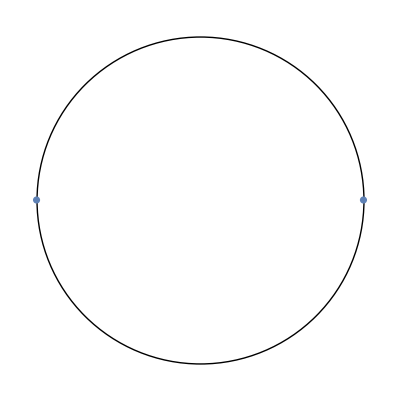

{}

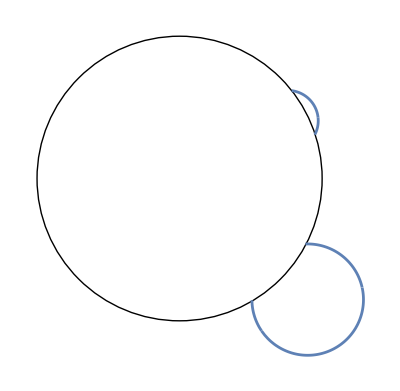

```mathematica
pointlst = globalPoints
n = Length[pointlst]
circle = Graphics[Circle[{0, 0}, 1]]
points = ListPlot[{{-1, 0}, {1, 0}}]
Show[circle, points]
bent = {}
For[i = 1, i≤n, i++, 
p1 = pointlst[[i]][[1]][[1]]+I*pointlst[[i]][[1]][[2]];
p2 = pointlst[[i]][[2]][[1]]+I*pointlst[[i]][[2]][[2]];
k = Norm[p1+p2];
const = (((2-k)/k)(p1+p2)-I(p1-p2))/(((2-k)/k)(p1+p2)+I(p1-p2));
c = Sqrt[(-2)/((p1-p2)(const^2+1))];
d = I*c*const;
a = (c(p1+p2)+d(p1-p2))/2;
b = (c(p1-p2)+d(p1+p2))/2;
f =(a+b)/(c+d);
t = Tan[p];
theta  = pointlst[[i]][[3]];
theta =-theta;
m =Limit[Tan[w], w->theta, Direction->"FromAbove"];
If[theta == -Pi/2, x = (t^2-4)/((-t+2)^2);
y = 0, If[theta == Pi/2, x=(t^2-4)/((2+t)^2); y=0,
x =(t^2+(m*t)^2-4)/(t^2+((m*t)+2)^2);
y = -4*t/(t^2+((m*t)+2)^2)]];
point = x+I*y;
fpoint = (a*point+b)/(c*point+d);
If[-Pi/2≤-theta≤Pi/2,bent = Join[bent, {ParametricPlot[{Re[fpoint], Im[fpoint]}, {p, 0, Pi/2}, PlotStyle->Automatic]}],
bent = Join[bent,{ParametricPlot[{Re[fpoint],Im[fpoint]}, {p, Pi/2, Pi}, PlotStyle->Automatic]}]]]
Show[circle,bent,  PlotRange->Full]
```